```mathematica
ClearAll["Global`*"]
```

```mathematica
σ[k_,x_,n_]:= KroneckerProduct[IdentityMatrix[2^(k-1)],PauliMatrix[x], IdentityMatrix[2^(n-k)]]
```

```mathematica
IsingHamiltonian[n_]:=Sum[σ[k,1,n].σ[Mod[k+1,n,1],1,n]+λ σ[k,3,n],{k,1,n}]
```

```mathematica
spectralgap[lst_]:= (Abs[#[[1]]-#[[2]]]&)[TakeSmallest[lst,2]]
```

```mathematica
λ12 = Monitor[Table[Eigenvalues[IsingHamiltonian[n]/.λ->1.2],{n,2,12,2}],n];
```

```mathematica
λ1 = Monitor[Table[Eigenvalues[IsingHamiltonian[n]/.λ->1.],{n,2,12,2}],n];
```

```mathematica
λ08= Monitor[Table[Eigenvalues[IsingHamiltonian[n]/.λ->0.8],{n,2,12,2}],n];
```

```mathematica
nlst=Table[n,{n,2,12,2}];
```

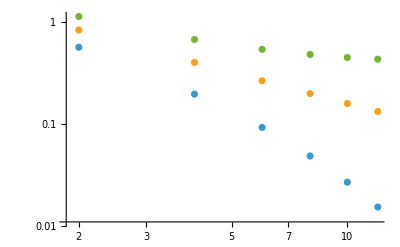

```mathematica
ListLogLogPlot[{Transpose[{nlst,spectralgap/@λ08}],Transpose[{nlst,spectralgap/@λ1}],Transpose[{nlst,spectralgap/@λ12}]}]
```

```mathematica
data={nlst, spectralgap/@λ08,spectralgap/@λ1,spectralgap/@λ12}//Transpose;
```

```mathematica
Export[NotebookDirectory[]<>"blatt12-data.csv",data]
```

C:\Users\junwe\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Complex Systems\blatt12-data.csv

```mathematica
spectralgap/@λ12
```

{1.1241,0.667735,0.535134,0.476265,0.445532,0.4281}

```mathematica
Mod[4,3,1]
```

1

```mathematica
IsingHamiltonian//MatrixForm
```

(3 λ | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | λ | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | λ | 0 | 1 | 0 | 0 | 1
1 | 0 | 0 | -λ | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | λ | 0 | 0 | 1
1 | 0 | 0 | 1 | 0 | -λ | 1 | 0
1 | 0 | 0 | 1 | 0 | 1 | -λ | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | -3 λ)

```mathematica
Eigenvalues[IsingHamiltonian]
```

{-1-λ,-1-λ,-1+λ,-1+λ,1+λ-2 √(1-λ+λ^2),1+λ+2 √(1-λ+λ^2),1-λ-2 √(1+λ+λ^2),1-λ+2 √(1+λ+λ^2)}

```mathematica
σ[1,3]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)